```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mode1Min=1;
mode1Max=10;
mode2Min=11;
mode2Max=20;
```

```mathematica
counts1={};
Do[
AppendTo[counts1,Import["lattice_v"<>IntegerString[i,10,2]<>"/counts/A.txt","Table"][[;;,2]]];
,{i,mode1Min,mode1Max,1}];
```

```mathematica
nns1={};
Do[
AppendTo[nns1,Import["lattice_v"<>IntegerString[i,10,2]<>"/nns/A_A.txt","Table"][[;;,2]]];
,{i,mode1Min,mode1Max,1}];
```

```mathematica
counts2={};
Do[
AppendTo[counts2,Import["lattice_v"<>IntegerString[i,10,2]<>"/counts/A.txt","Table"][[;;,2]]];
,{i,mode2Min,mode2Max,1}];
```

```mathematica
nns2={};
Do[
AppendTo[nns2,Import["lattice_v"<>IntegerString[i,10,2]<>"/nns/A_A.txt","Table"][[;;,2]]];
,{i,mode2Min,mode2Max,1}];
```

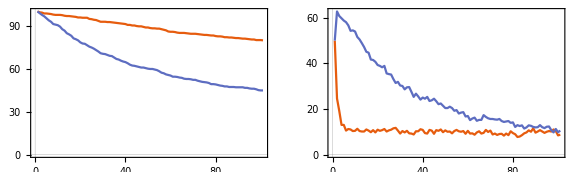

```mathematica
GraphicsRow[{
ListLinePlot[{Mean[counts1]//N,Mean[counts2]//N},PlotRange->All],
ListLinePlot[{Mean[nns1]//N,Mean[nns2]//N},PlotRange->All]
},ImageSize->Large]
```

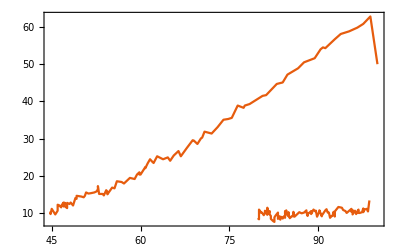

```mathematica
Show[
ListLinePlot[Transpose[{Mean[counts1]//N,Mean[nns1]//N}]],
ListLinePlot[Transpose[{Mean[counts2]//N,Mean[nns2]//N}]]
,PlotRange->All]
```